# the workload test report

```mathematica
SetDirectory[NotebookDirectory[]];
plotrange = {0,1300000};
VMPlot[vm_,label_] := ListLinePlot[vmᵀ[[{3,5,7}]],
PlotRange->plotrange,
PlotLabel->label,
PlotLegends->{"total","used","free"}]
VMPlot[vm_] := VMPlot[vm,""]
(*rotate left*)
rl[d_]:=Placed[d,Axis,Rotate[#,Pi/2]&]
```

#### test 1 mono date:01-02

**参数**:2台虚拟机,mono从50M到400M

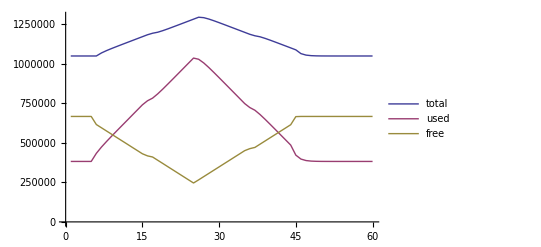
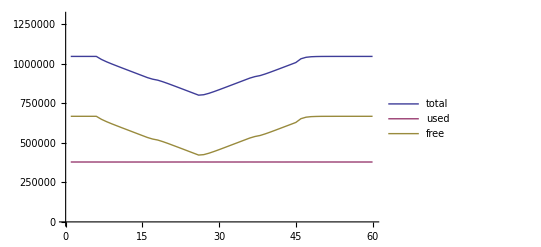
-Graphics- | -Graphics-

```mathematica
vm6 = Import["../dataset/1-2_mono_50M~400M/8.log"][[4;;]];
vm7 = Import["../dataset/1-2_mono_50M~400M/9.log"][[4;;]];
{{VMPlot[vm6],VMPlot[vm7]}}//TableForm
```

三条线依次是总内存分配(蓝),可用内存(黄),使用内存(红).
从图中可以得出:随着使用量的增大.调节程序从空闲机器中取走一部分内存.
给了负载机.而且取走的内存并不严格等于请求的内存.因为负载机的可用内存也在减小.
这个就是由τ值控制的.

#### test 2 mono date:01-04

**参数**:5台虚拟机,mono从50M到400M

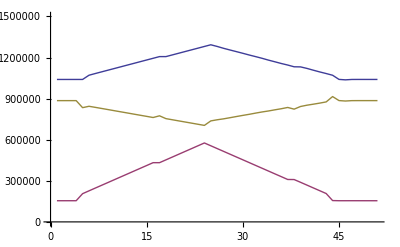
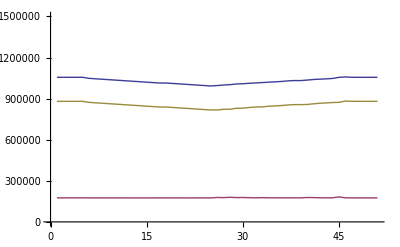
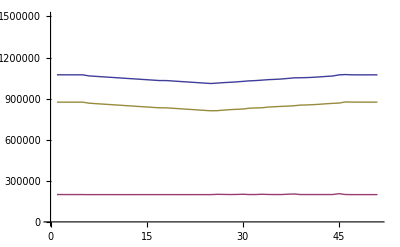
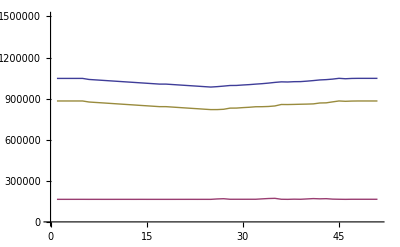
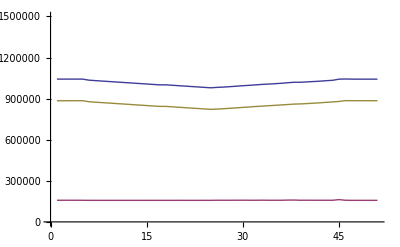
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
vm1 = Import["../dataset/1-4_mono_5VM/8.log"][[4;;]];
vm2 = Import["../dataset/1-4_mono_5VM/9.log"][[4;;]];
vm3 = Import["../dataset/1-4_mono_5VM/10.log"][[4;;]];
vm4 = Import["../dataset/1-4_mono_5VM/11.log"][[4;;]];
vm5 = Import["../dataset/1-4_mono_5VM/12.log"][[4;;]];
plotrange = {0,1500000};
{{VMPlot[vm1],VMPlot[vm2]},{VMPlot[vm3],VMPlot[vm4]},{VMPlot[vm5]}}//TableForm
```

为了能够更好的测量,将虚拟机台数增大到5台.看调节程序是否能正确的处理.
从结果可以看到.和2台时候类似,4台空闲机的总内存都有微小的下降.
这是因为.经过调节之后.从4台空闲机上均分了1台负载机的内存要求.

#### test 3 dacapo date:01-08

```mathematica
dacapo=Import["../dataset/1_8_dacapo/dacapo.csv"][[4;;All]];
```

**参数**:低负载,开启调节和不开启调节

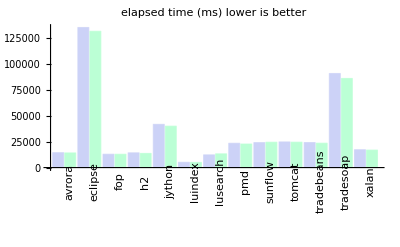
-Graphics--Graphics- | Off
-Graphics- | on

```mathematica
BarChart[dacapo[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

由图中得出.在低负载情况下.无论是否开启内存.对CPU影响都不大.
都能够保持高效的运算.

======================depreciated=====================
eat 400M;

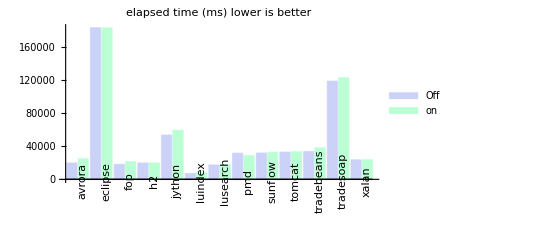

```mathematica
BarChart[dacapo[[All,4;;5]],
ChartLabels->{rl[dacapo[[All,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

eat 800M;no adjust first

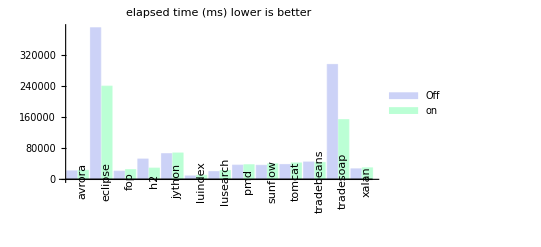

```mathematica
BarChart[dacapo[[All,6;;7]],
ChartLabels->{rl[dacapo[[All,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

eat 800M again;adjust first

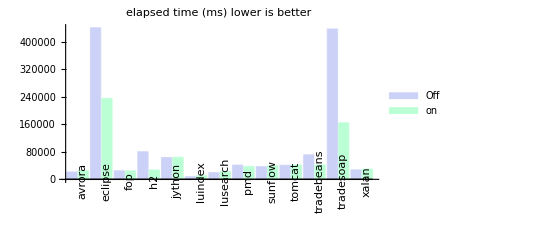

```mathematica
BarChart[dacapo[[All,8;;9]],
ChartLabels->{rl[dacapo[[All,1]]],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

====================================================

#### test 4 dacapo date:01-09

```mathematica
swapoff=Import["../dataset/1-9_dacapo/swap-off.log"][[3;;All,5]];
swapon=Import["../dataset/1-9_dacapo/swap-on.log"][[3;;All,5]];
dacapo = Import["../dataset/1-9_dacapo/dacapo.csv"][[2;;All]];
vm1 = Import["../dataset/1-9_dacapo/1.log"][[4;;]];
vm2 = Import["../dataset/1-9_dacapo/2.log"][[4;;]];
vm3 = Import["../dataset/1-9_dacapo/3.log"][[4;;]];
vm4 = Import["../dataset/1-9_dacapo/4.log"][[4;;]];
vm5 = Import["../dataset/1-9_dacapo/5.log"][[4;;]];
```

**参数**:高负载(800M),开启调节和不开启调节

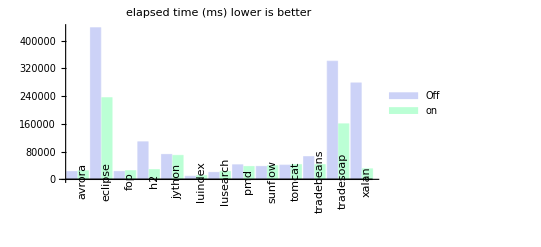

```mathematica
BarChart[dacapo[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"Off","on"},PlotLabel->"elapsed time (ms) lower is better"]
```

由图中看出.在高负载情况下.开启调节能够大幅度的减少执行时间.
和上图对比,完全来说.是在高负载情况下.程序执行时间大幅增加.而经过调节程序.
能够减缓这种增加趋势.在所有测试中.差距明显的是
eclipse,h2,trade beans,trade scope,xalan.
通过附录中对dacapo测试表格的描述可以知道.这些都是内存集中型的.
而CPU集中型的.差距都不是很明显.基本可以忽略.

为了更好的探究其中的原因.参见下图:

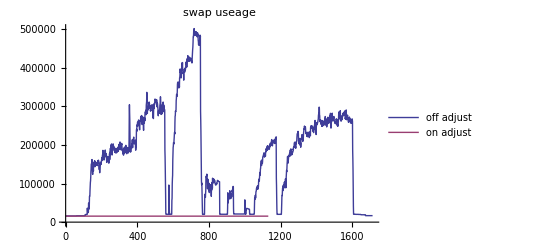

```mathematica
ListLinePlot[{swapoff,swapon},
PlotLabel->"swap useage",
PlotLegends->{"off adjust","on adjust"}]
```

其中蓝色的线条是不开启调节时候.SWAP的占用率.而下面不是非常明显的红色的线条
是开启调节时候的SWAP占用率.

该图有以下的解读:
* 红色的线条比蓝色的短:

>说明开启调节后测试所需要的时间比不开启的短.因为记录是相同的单位时间.
>记录是在测试执行完之后就关闭了.记录的数量少,则总时间就短.
>这个结论和上图中内存集中型测试耗时更少是一致的.

* 红色线条基本没有变化:

>说明开启调节后SWAP分区基本没有使用增加.这个和图1进行参考.知道了因为调节
>程序为负载机分配了更多的内存.使得虽然负载机可用内存依然减少了.但是还完全
>不需要使用SWAP分区.

* 蓝色线条变化剧烈:

>说明不开启调节巨量的使用SWAP分区.因为负载程序的参数是800M.内存一共1000M,
>系统使用100多M.剩下的不足60M.也就是说,负载机已经完全没有什么内存空间执行
>dacapo测试了.所以这个时候只能全部的向SWAP分区申请空间来运行dacapo.

* 不开启调节大量使用SWAP:

>由上面3条结论.我们不难得出负载机器在高负载情况下.开启调节和不开启调节.
>对于内存集中型测试运行时间差异巨大的真正原因:
>不开启调节的时候大量使用SWAP分区.开启调节不用使用SWAP分区.
>SWAP分区的访问速度等于磁盘的访问速度是和内存的访问速度完全不是一个数量级.
>所以导致了不开启调节的时候.消耗时间巨幅增加.

为了探究在开启调节后.负载机没有使用SWAP分区的原因.
参见下图:

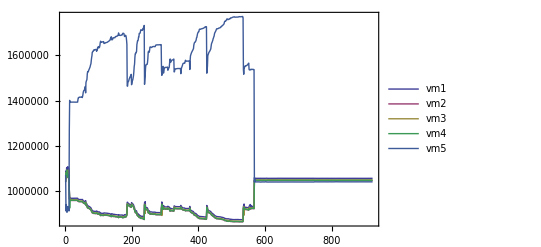

```mathematica
ListLinePlot[{vm1[[All,3]],vm2[[All,3]],vm3[[All,3]],vm4[[All,3]],vm5[[All,3]]},
Frame->True,PlotRange->All,
PlotLegends->{"vm1","vm2","vm3","vm4","vm5"}
]
```

该图是在调节时候调节程序记录下来的对所有内存的分配.
等效于实验2中.5个虚拟机的总内存变化曲线的集合.
其中非常突出的曲线是负载机的内存变化.非常的夸张.
剩下4条比较相近的是4台空闲机的内存变化.
中间的分割线是10^6KB,也就是1000MB.

该图时间序有3个阶段:

* 开启调节程序`mm_server`
  此时,经过短暂的震荡,内存数值由调节程序接管.
  调节程序通过各个虚拟机的使用量,计算并赋予新的内存分配.
  负载机内存变化到800M(因为此时刚刚运行完无调节的测试,
  系统内存全部释放完了.所以系统内存只使用了100MB,而其他空闲机.
  系统保持一定的缓存,均在200MB~300MB之间)
* 开启负载程序`mm_test_static 800M`
  此时.负载机器内存很快到达1400MB.并维持不变.
  其他各个机器内存使用均跌至950MB.
  负载机增量$1400-800=600$.
  空闲机负增量$(1100-950)*4=600$.所以也是平衡的.虽然从图上.
  有些视错觉.
* 开启dacapo测试程序.
  经过短暂的时间.是人工反应时间.是测试者从开启负载程序到开启
  dacapo测试程序的自然时间.然后在长时间的范围上.都是dacapo的运行
  时间.而且结合图3,内存分配图上.有一个非常明显的特点.
  就是开启调节时候总内存分配图趋势和不开启调节时候SWAP占用率.
  两者是惊人的一致.
  事实上开启调节时候.负载机总内存的分布有以下关系
  $$总内存=系统占用内存+负载程序内存+dacapo运行内存+剩余内存$$
  其中因为是高负载.系统把所有缓存都让出来了.系统占用内存约为100MB且不变.
  负载程序内存是固定的800M.
  剩余内存不多.大概为60M.dacapo运行内存就是如同图上的波动.随时间变化.
  不恒定.
  SWAP空间在开启调节时候基本没有使用.所以不作考虑.
  另外.我们也可以得出结论:
    + 不开启调节时候SWAP占用量和开启调节时候总内存分配趋势一致.
      换一种说法.总内存扣除负载程序内存和系统占用内存和剩余内存
      基本上等于不开启调节时候的SWAP占用量.
    + 开启调节以后因为调节程序为负载机分配了足量的内存.以至于负载机可以
      不必使用SWAP分区.亦即大幅度的抑制性能的损失.
      在调节过程中.4台空闲机的内存变化和负载机的内存变化基本反比一致.
  并且4台空闲机变化一致.这个和图1,图2的结论是一致的.
  综上:我们最终能够描绘内存的移动:
    + 不开启调节情况下:系统和负载程序基本把总内存占用完了.
      dacapo运行必须借助于SWAP分区.
    + 开启调节情况下:系统和负载程序基本把总内存占用完了的时候.
      调节程序又从其他空闲机器中抽走了内存.并补充给负载机器足
      量内存.所以在dacapo运行时候可以不用使用SWAP分区.所以可以
      减少性能的损失.
* dacapo测试运行完成
  此时,总内存分配再次回到1500MB水平并持续.至于为什么不是
  1400MB.因为负载机并不能完全回到之前的完全一致的条件.
  在开始的时候内存使用量为900MB,结束测试后,内存使用量为1200MB
* 关闭负载程序
  此时负载机内存使用量迅速跌至1050MB左右.同时,其他空闲机的内存
  也恢复至同样的水平.此后很长时间保持不变.

#### test 5 τ test, date:0-28

```mathematica
dp = Import["../dataset/1-28_tau/dacapo.csv"][[2;;]];
Subscript[vm1, 0.75]=Import["../dataset/1-28_tau/0.75_1.log"][[4;;]];
Subscript[vm2, 0.75]=Import["../dataset/1-28_tau/0.75_2.log"][[4;;]];
Subscript[vm3, 0.75]=Import["../dataset/1-28_tau/0.75_3.log"][[4;;]];
Subscript[vm4, 0.75]=Import["../dataset/1-28_tau/0.75_4.log"][[4;;]];
Subscript[vm5, 0.75]=Import["../dataset/1-28_tau/0.75_5.log"][[4;;]];

Subscript[vm1, 1]=Import["../dataset/1-28_tau/1.0_1.log"][[4;;]];
Subscript[vm2, 1]=Import["../dataset/1-28_tau/1.0_2.log"][[4;;]];
Subscript[vm3, 1]=Import["../dataset/1-28_tau/1.0_3.log"][[4;;]];
Subscript[vm4, 1]=Import["../dataset/1-28_tau/1.0_4.log"][[4;;]];
Subscript[vm5, 1]=Import["../dataset/1-28_tau/1.0_5.log"][[4;;]];
```

因为τ仅仅是一个线性变化的量.导致以它找到最值比较困难.
下图是根据不同的τ值测量出来的dacapo对比测试.(高负载800M)
从结果中可以看到.在τ=1.0的情况下.有微小的提升.

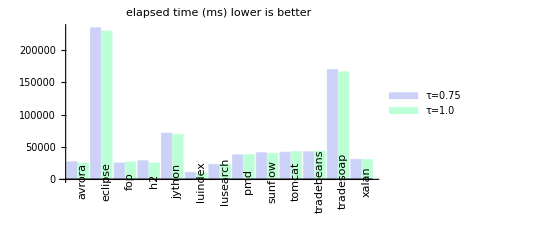

```mathematica
BarChart[dp[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"τ=0.75","τ=1.0"},PlotLabel->"elapsed time (ms) lower is better"]
```

从内存分配图上更能体现,为了不产生误导,认为τ=1.0的情况比0.75时候分配了比较明显差异的内存.
选取从0开始的做图范围.
从结果中可以看到.因为τ=1.0分配了更多的内存.所以完成时间也有所提前.

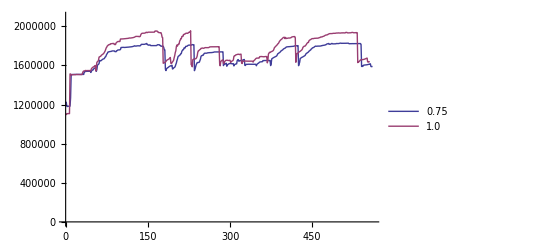

```mathematica
ListLinePlot[{Subscript[vm5, 0.75][[1;;560,3]],Subscript[vm5, 1][[1;;555,3]]},PlotRange->{0,2100000},PlotLegends->{"0.75","1.0"}]
```

======================unused==================================

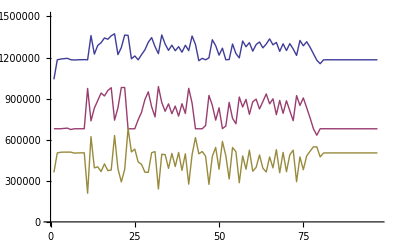
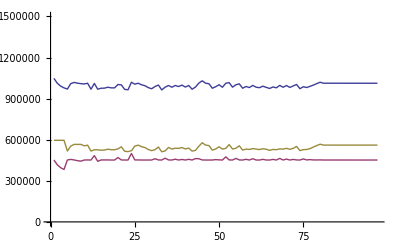
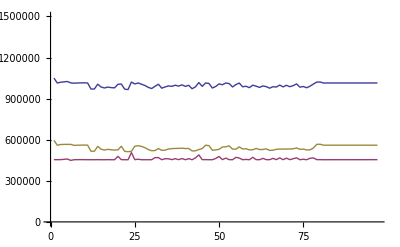
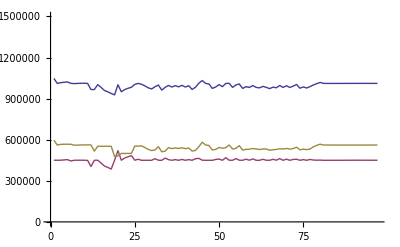
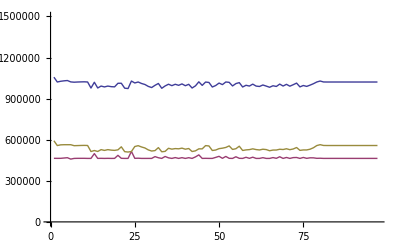
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- |

```mathematica
vm1 = Import["../dataset/1-21_random_0.75/1.log"][[4;;]];
vm2 = Import["../dataset/1-21_random_0.75/2.log"][[4;;]];
vm3 = Import["../dataset/1-21_random_0.75/3.log"][[4;;]];
vm4 = Import["../dataset/1-21_random_0.75/4.log"][[4;;]];
vm5 = Import["../dataset/1-21_random_0.75/5.log"][[4;;]];
plotrange = {0,1500000};
{{VMPlot[vm1],VMPlot[vm2]},{VMPlot[vm3],VMPlot[vm4]},{VMPlot[vm5]}}//TableForm
```

```mathematica
vm1 = Import["../dataset/1-21_random_1/1.log"][[4;;]];
vm2 = Import["../dataset/1-21_random_1/2.log"][[4;;]];
vm3 = Import["../dataset/1-21_random_1/3.log"][[4;;]];
vm4 = Import["../dataset/1-21_random_1/4.log"][[4;;]];
vm5 = Import["../dataset/1-21_random_1/5.log"][[4;;]];
plotrange = {0,1500000};
{{VMPlot[vm1],VMPlot[vm2]},{VMPlot[vm3],VMPlot[vm4]},{VMPlot[vm5]}}//TableForm
```

1-28 compare test about τ value
===============================================================

## redo all test under τ=1.0 condition

### 02-03:monotest,2 machine ;50M ~ 400M

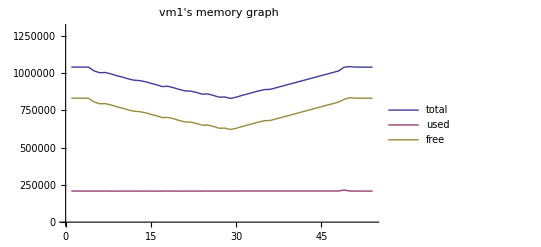
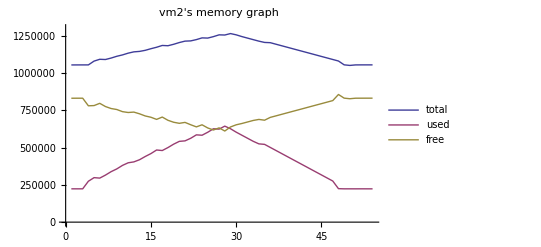

```mathematica
vm1=Import["../dataset/2-3_mono_2/1.log"][[4;;]];
vm2=Import["../dataset/2-3_mono_2/2.log"][[4;;]];
g=Partition[{VMPlot[vm1,"vm1's memory graph"],VMPlot[vm2,"vm2's memory graph"]},1]//TableForm
Export["graph/mono_2.png",g,ImageResolution->150,ImageSize->800];
```

### 02-03: monotest 5 machine; 50M~400M

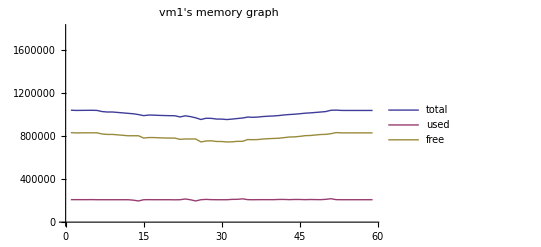
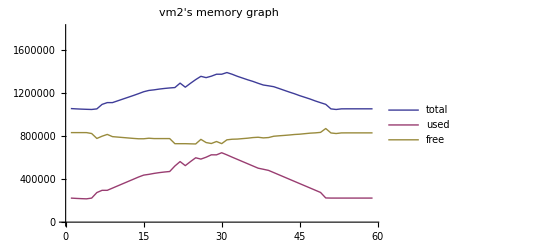
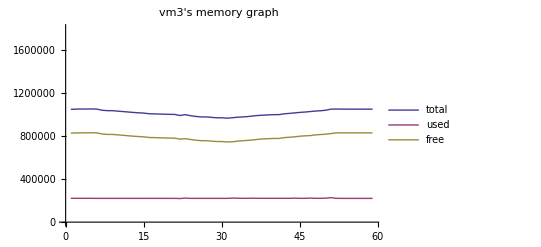
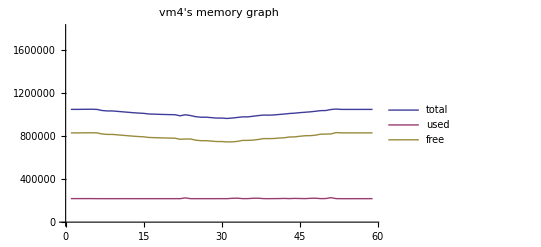
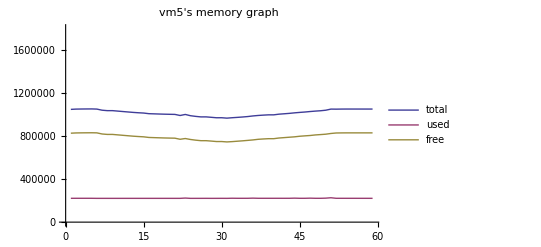

```mathematica
vm1=Import["../dataset/2-3_mono_5/1.log"][[4;;]];
vm2=Import["../dataset/2-3_mono_5/2.log"][[4;;]];
vm3=Import["../dataset/2-3_mono_5/3.log"][[4;;]];
vm4=Import["../dataset/2-3_mono_5/4.log"][[4;;]];
vm5=Import["../dataset/2-3_mono_5/5.log"][[4;;]];
plotrange={0,1800000};
g={{VMPlot[vm1,"vm1's memory graph"]},{VMPlot[vm2,"vm2's memory graph"]},
{VMPlot[vm3,"vm3's memory graph"]},{VMPlot[vm4,"vm4's memory graph"]},
{VMPlot[vm5,"vm5's memory graph"]}}//TableForm
Export["graph/mono_5.png",g,ImageResolution->150];
```

### 02-03;datapo test;low

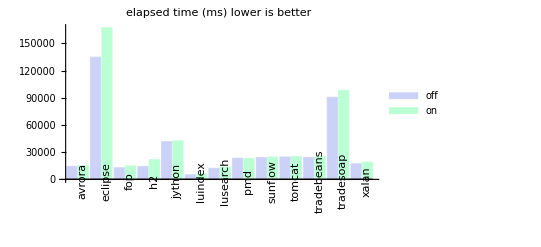

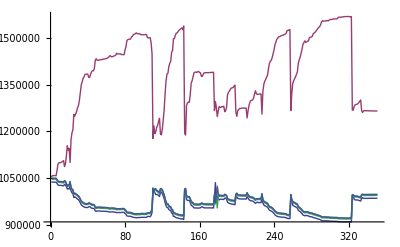

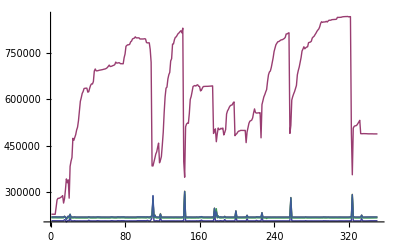

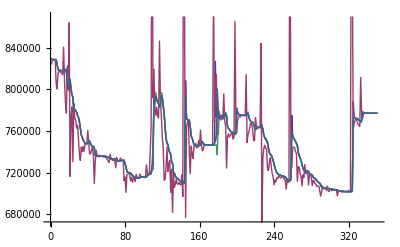

```mathematica
dp = Import["../dataset/2-3_dacapo_low/dacapo.csv"][[2;;]];
vm1=Import["../dataset/2-3_dacapo_low/1.log"][[4;;]];
vm2=Import["../dataset/2-3_dacapo_low/2.log"][[4;;]];
vm3=Import["../dataset/2-3_dacapo_low/3.log"][[4;;]];
vm4=Import["../dataset/2-3_dacapo_low/4.log"][[4;;]];
vm5=Import["../dataset/2-3_dacapo_low/5.log"][[4;;]];
BarChart[dp[[All,2;;3]],
ChartLabels->{Placed[dacapo[[All,1]],Axis,Rotate[#,Pi/2]&],None},
ChartLegends->{"off","on"},PlotLabel->"elapsed time (ms) lower is better"]
ListLinePlot[{vm1[[All,3]],vm2[[All,3]],vm3[[All,3]],vm4[[All,3]],vm5[[All,3]]}]
ListLinePlot[{vm1[[All,5]],vm2[[All,5]],vm3[[All,5]],vm4[[All,5]],vm5[[All,5]]}]
ListLinePlot[{vm1[[All,7]],vm2[[All,7]],vm3[[All,7]],vm4[[All,7]],vm5[[All,7]]}]
```

### 02-04 ; tau test

上面介绍了dacapo测试.其中值域仅仅是时间t.具有方便直观的比较的特点.
在上面通过理论推导了τ的一些性质.发现τ值的影响主要包括线性,范围不断增大的特点.
为了更加具体的研究τ实际中的情况.所以通过dacapo测试对τ进行连续性的测试.

测试方法:

基本和dacapo高负荷测试一样.首先使用负载程序占用800M的内存.然后再开启swap记录程序.和dacapo测试程序.
这里自变量为τ.
通过对每个测试使用时间的记录和内存分配的记录和swap占用情况的记录.来研究不同的τ值带来的具体的影响.

为了保证公平性.每进行完成一个测试.让虚拟机重启,然后再进行下一次测试工作.保证每次测试的时候虚拟机都是同一初始状态.

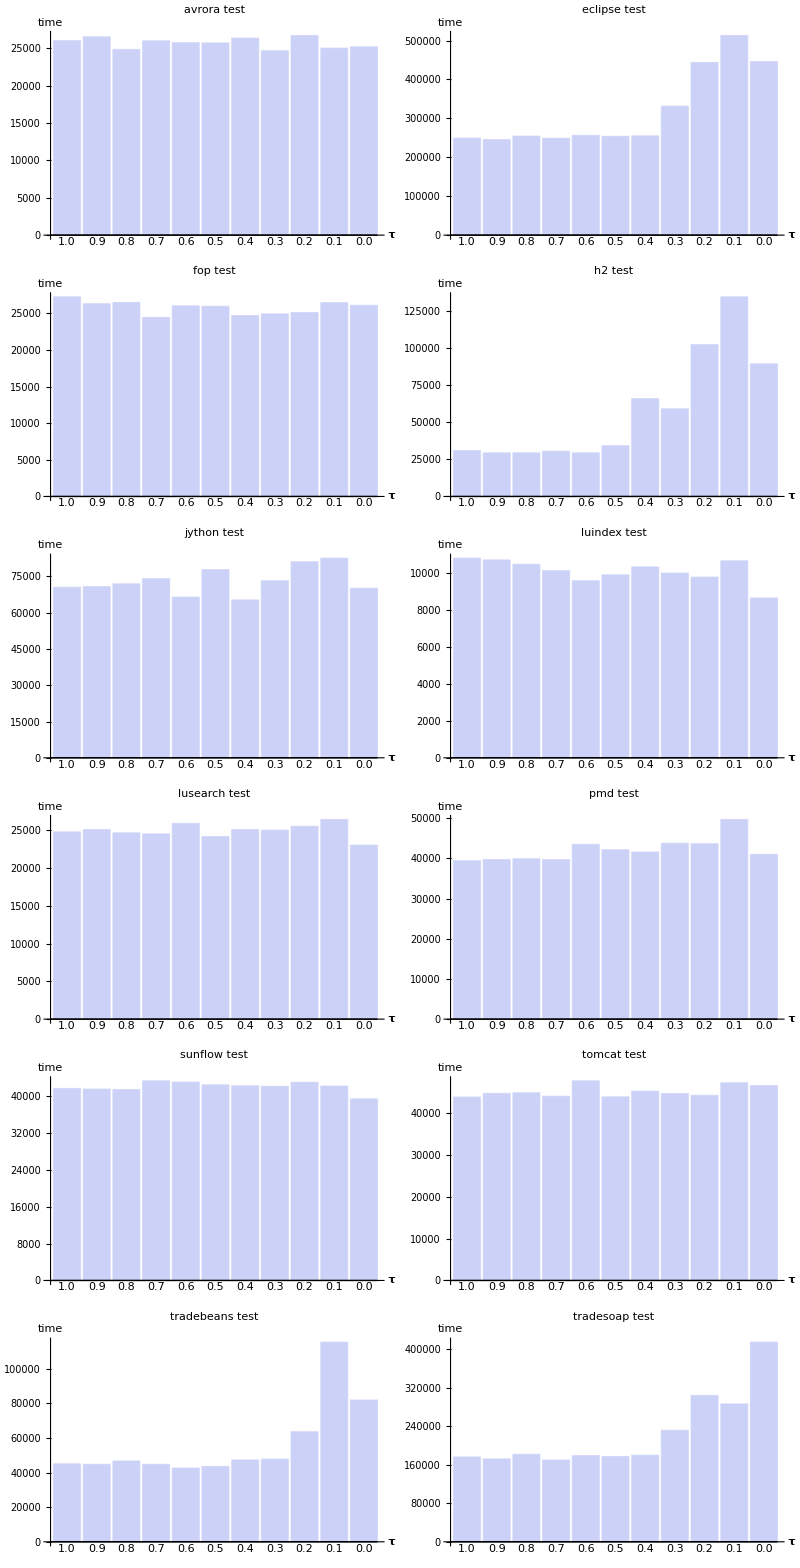

```mathematica
dacapo=Import["../dataset/2-4_tau/dacapo.csv"][[2;;-2,{1,9,8,7,6,5,10,11,12,13,15,16}]];
Partition[Table[BarChart[dacapo[[i,2;;]],
ChartLabels->{"1.0","0.9","0.8","0.7","0.6","0.5","0.4","0.3","0.2","0.1","0.0"},
AxesLabel->{"τ","time"},
PlotLabel->dacapo[[i,1]]<>" test",ImageSize->{300}]
,{i,Length[dacapo]}],2]//TableForm
```

从不同的测试集的结果可以看出.不同的测试对内存的要求偏向.非常明显的.

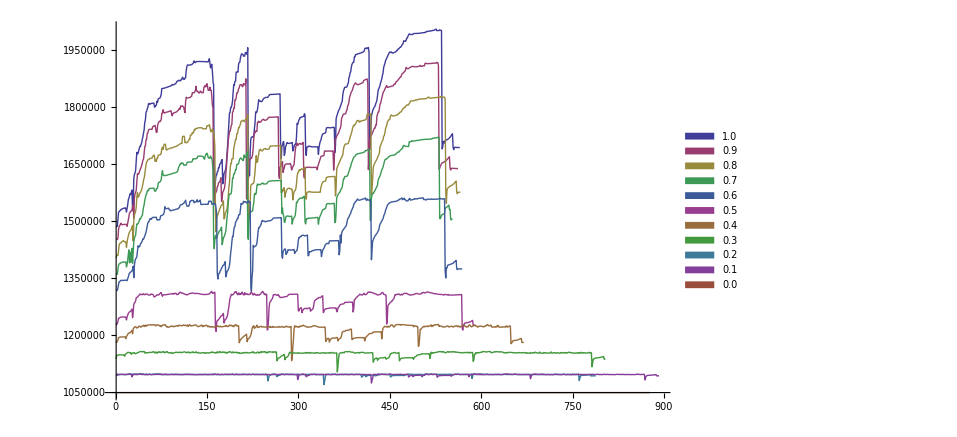

```mathematica
vm1=Import["../dataset/2-4_tau/1.0.log"][[4;;]];
vm2=Import["../dataset/2-4_tau/0.9.log"][[4;;]];
vm3=Import["../dataset/2-4_tau/0.8.log"][[4;;]];
vm4=Import["../dataset/2-4_tau/0.7.log"][[4;;]];
vm5=Import["../dataset/2-4_tau/0.6.log"][[4;;]];
vm6=Import["../dataset/2-4_tau/0.5_2.log"][[4;;]];
vm7=Import["../dataset/2-4_tau/0.4.log"][[4;;]];
vm8=Import["../dataset/2-4_tau/0.3.log"][[4;;]];
vm9=Import["../dataset/2-4_tau/0.2.log"][[4;;]];
vm10=Import["../dataset/2-4_tau/0.1.log"][[4;;]];
vm11=Import["../dataset/2-4_tau/0.0.log"][[4;;]];
ListLinePlot[{vm1[[All,3]],vm2[[All,3]],vm3[[All,3]],vm4[[All,3]],vm5[[All,3]],vm6[[All,3]],
vm7[[All,3]],vm8[[All,3]],vm9[[All,3]],vm10[[All,3]],vm11[[All,3]]},
PlotRange->All,
PlotLegends->SwatchLegend[{"1.0","0.9","0.8","0.7","0.6","0.5","0.4","0.3","0.2","0.1","0.0"}]
]
```

从结果可以首先看出τ的线性性质.随着τ从0到1的变化,分配的内存也越来越多.
其次可以看出在τ从0到0.6的时候有很多区域是平的.这个是因为达到τ的最大值限制了.
因为τ在不同的取值的时候,变化范围即[Min,Max]也是不断扩展开.当实际需求的内存超过这个范围.则被强制截断.
剩下不足的内存就从swap分区中取用.

在τ从0到0.5的时候可以看出.执行时间基本上随着τ的增大而不断变小.
而且变化趋势基本上是线性的.
但是当τ超过0.5之后.虽然总的内存随着τ不断的增加.但是执行时间在误差范围之内基本上不变.
但这绝非说明τ一直设置为0.6就足够了.这仅仅
说明τ=0.6即是本次测试(static 800M+dacapo)的阈值.超过这个值之后.τ的增加并没有实质上的提高.
分配的内存超过实际需要的内存.使得分配的越多.可用的内存越多.分配得越多并没有什么实质性的作用

但是可想而知.如果是面临内存需求更高的应用环境.这个临界阈值也在不断的增加.
结合之前的可行域的思想.我们可以知道.可行域中.可行域范围是随着τ的增加而不断增加的.
在实际环境中.当τ<1时候任何一个不可行的点的具体表现是:
提出的内存超过最大值界线.实际分配的内存小于需求的内存.使得可用内存为负值.而实际上这个负值就是swap分区的使用量.
当τ等于1的时候.尽量的使得不使用swap分区.但是实际上对于使用内存没有到临界情况的时候.也会有过度分配的现象.
具体表述是:这个时候τ在1的邻域范围内.其性能都是一样的.没有变化.但是对于内存使用比较多的会分配更多的总内存,使得可用内存
也相对使用的量而言也比较多.但是另外一些明明没有怎么使用内存的虚拟机,其可用内存相对自身而言则比较少了.
而当τ=1的时候则是非常明显的."所有虚拟机的可用内存均相等".将这种情况表达到了极端.

因为之前讨论.这种现象并不会带来性能上的提升,同样也不会带来性能上的下降.所以可以不用管它.

另外可以看到在τ=1的时候.极端情况下.内存分配达到了2000MB.对于整个实验来讲.这个值并不是什么特殊的数值.
即没有达到τ=1的最大分配5000MB.也不是任何临界条件.

但是.2000这个数值达到了xen设置的静态最大值.当以后内存分配超过2000之后.实际上xen也只会分配2000MB.
所以从此之后的的分配就没有意义了.
而要改变这个静态最大值.必须停机设置才有效.限制了内存调节的范围.

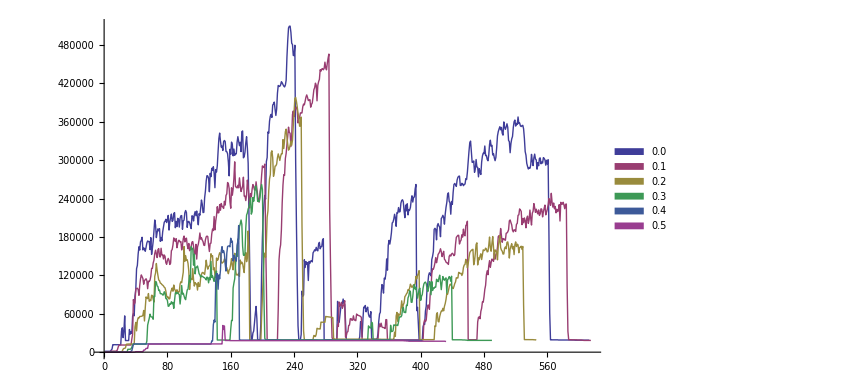

```mathematica
swap1=Import["../dataset/2-4_tau/0.5_2_swap.log"][[3;;All,5]];
swap2=Import["../dataset/2-4_tau/0.4_swap.log"][[3;;All,5]];
swap3=Import["../dataset/2-4_tau/0.3_swap.log"][[3;;All,5]];
swap4=Import["../dataset/2-4_tau/0.2_swap.log"][[3;;All,5]];
swap5=Import["../dataset/2-4_tau/0.1_swap.log"][[3;;All,5]];
swap6=Import["../dataset/2-4_tau/0.0_swap.log"][[3;;615,5]];
ListLinePlot[{swap6,swap5,swap4,swap3,swap2,swap1},
PlotLegends->SwatchLegend[{"0.0","0.1","0.2","0.3","0.4","0.5"}]]
```

从swap分区使用量来看也能得到类似的结论.即随着τ的增加.swap使用量越来越少.
记录只有0到0.5的数值.之后的数值因为几乎接近于0所以没有作图.
考虑到上一个图中从0.6到1的时候.性能几乎没有什么变化.这也是能够理解的.因为他们都有swap分区使用量为0这个共同点.